```mathematica
(* Start with V = const *)
```

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2 1==0,y''[t]+(3 x'[t]y'[t])/x[t]+0==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433328, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

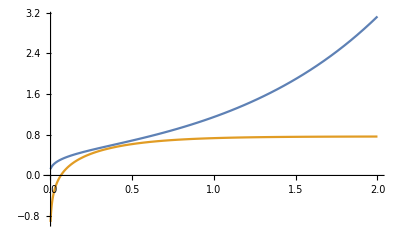

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```

```mathematica
(* now try v = phi^2 *)
```

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2(y[t])^2==0,y''[t]+(3 x'[t]y'[t])/x[t]+y[t]==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433326, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

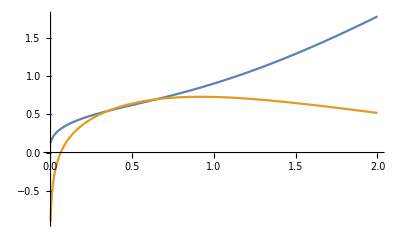

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```